```mathematica
Clear["Global`*"]
(*Define the fields and frequency *)
η[x_,t_,ϵ_] := Subscript[η, 0][x,t] + ϵ Subscript[η, 1][x,t] + ϵ^2/2 Subscript[η, 2][x,t];
ϕ[x_,y_,t_,ϵ_] := Subscript[ϕ, 0][x,y,t] + ϵ Subscript[ϕ, 1][x,y,t] + ϵ^2/2 Subscript[ϕ, 2][x,y,t];
ω[ϵ_] := Subscript[ω, 0]  + ϵ^2/2 Subscript[ω, 2];
 VdW = -h/3(1/(1 + ϵ  η[x,t,ϵ]/h)^3-1);
Series[VdW,{ϵ,0,3}]//Normal
```

ϵ η_0[x,t]+(ϵ^2 (-2 η_0[x,t]^2+h η_1[x,t]))/h-(ϵ^3 (-20 η_0[x,t]^3+24 h η_0[x,t] η_1[x,t]-3 h^2 η_2[x,t]))/(6 h^2)

```mathematica
Eq2= -h/3(1/(1 + ϵ  η[x,t,ϵ]/h)^3-1) +ϵ ω[ϵ] D[ϕ[x,y,t,ϵ],t] + 1/2 ϵ^2 ((D [ϕ[x,y,t,ϵ],x])^2 +  (D [ϕ[x,y,t,ϵ],y])^2 ) ;
Eq2g= η[x,t,ϵ] + ω[ϵ] D[ϕ[x,y,t,ϵ],t] + 1/2 ϵ ((D [ϕ[x,y,t,ϵ],x])^2 +  (D [ϕ[x,y,t,ϵ],y])^2 ) ;
Eq3= -D[ϕ[x,y,t,ϵ],y] + ω[ϵ] D[η[x,t,ϵ],t] + ϵ D[ϕ[x,y,t,ϵ],x]D[η[x,t,ϵ],x]  ;
```

```mathematica
Eq2ZeroOrder = D[Eq2/.{y -> ϵ η [x,t,ϵ]},{ϵ,1}]/.{ϵ -> 0}//Expand
Eq2FirstOrder=1/2 D[Eq2/.{y -> ϵ η [x,t,ϵ]},{ϵ,2}]/.{ϵ -> 0}//Expand
Eq2SecondOrder =1/3 D[Eq2/.{y -> ϵ η [x,t,ϵ]},{ϵ,3}]/.{ϵ -> 0}//Expand
```

η_0[x,t]+ω_0 ϕ_0^(0,0,1)[x,0,t]

-(2 η_0[x,t]^2)/h+η_1[x,t]+ω_0 ϕ_1^(0,0,1)[x,0,t]+1/2 (ϕ_0^(0,1,0)[x,0,t])^2+ω_0 η_0[x,t] ϕ_0^(0,1,1)[x,0,t]+1/2 (ϕ_0^(1,0,0)[x,0,t])^2

(20 η_0[x,t]^3)/(3 h^2)-(8 η_0[x,t] η_1[x,t])/h+η_2[x,t]+ω_2 ϕ_0^(0,0,1)[x,0,t]+ω_0 ϕ_2^(0,0,1)[x,0,t]+2 ϕ_0^(0,1,0)[x,0,t] ϕ_1^(0,1,0)[x,0,t]+2 ω_0 η_1[x,t] ϕ_0^(0,1,1)[x,0,t]+2 ω_0 η_0[x,t] ϕ_1^(0,1,1)[x,0,t]+2 η_0[x,t] ϕ_0^(0,1,0)[x,0,t] ϕ_0^(0,2,0)[x,0,t]+ω_0 η_0[x,t]^2 ϕ_0^(0,2,1)[x,0,t]+2 ϕ_0^(1,0,0)[x,0,t] ϕ_1^(1,0,0)[x,0,t]+2 η_0[x,t] ϕ_0^(1,0,0)[x,0,t] ϕ_0^(1,1,0)[x,0,t]

```mathematica
Test1 = D[(Eq2 )/. {y-> ϵ η[x,t,ϵ]},{ϵ,3}]/.{ϵ -> 0}//Expand;
Test3 = D[ Eq3/.{y -> ϵ η[x,t,ϵ]},{ϵ,2}]/.{ϵ -> 0 };
expr =(Subscript[ω, 0]/3 D[Test1,t] == Test3)/.{Subscript[ϕ, 0] -> Function[{x,y,t},Subscript[ω, 0]/Sinh[h] Cos[t] Cos[x] Cosh[y+h]],
 Subscript[η, 0] -> Function [{x,t},Cos[x]Sin[t]] ,
Subscript[ϕ, 1] -> Function[{x,y,t}, Subscript[β, 0] + 1/8(Subscript[ω, 0] - Subscript[ω, 0]^-3 + 4/h Subscript[ω, 0]^-1)t - 1/16(3 Subscript[ω, 0]+Subscript[ω, 0]^-3+4/h Subscript[ω, 0]^-1)Sin [2t]  - 3/(16 Cosh[2 h])Subscript[ω, 0]^-7(Subscript[ω, 0]^4+1)(Subscript[ω, 0]^4-1 + 4/(3h)Subscript[ω, 0]^2)Sin[2t]Cos[2 x] Cosh[2(y+h)]],
Subscript[η, 1] -> Function [{x,t},1/8((Subscript[ω, 0]^2 + Subscript[ω, 0]^-2 + 4/h)+ (Subscript[ω, 0]^-2 - 3 Subscript[ω, 0]^-6 + 4/h Subscript[ω, 0]^-4)Cos[2t])Cos[2x] ]} ;
```

```mathematica
expr2 = expr /.{Coth[h] -> Subscript[ω, 0]^-2}/.{Tanh[2h] -> (2 Tanh[h])/(1 + Tanh[h]^2)}/.{Tanh[h] -> Subscript[ω, 0]^2}//Expand//Simplify//Expand
FourierCosSeries[1/(8h Subscript[ω, 0]^6)((12 h Cos[t] Cos[x])/Subscript[ω, 0]-(36 h Cos[t] Cos[2 t] Cos[x])/Subscript[ω, 0]+(27 h Cos[t] Cos[2 (t-x)] Cos[x])/Subscript[ω, 0]-(24 h Cos[t] Cos[x] Cos[2 x])/Subscript[ω, 0]+(27 h Cos[t] Cos[x] Cos[2 (t+x)])/Subscript[ω, 0]-16 Cos[t] Cos[x] Subscript[ω, 0]+48 Cos[t] Cos[2 t] Cos[x] Subscript[ω, 0]-72 Cos[t] Cos[2 (t-x)] Cos[x] Subscript[ω, 0]+80 Cos[t] Cos[x] Cos[2 x] Subscript[ω, 0]-72 Cos[t] Cos[x] Cos[2 (t+x)] Subscript[ω, 0]+4 h Cos[t] Cos[x] Subscript[ω, 0]^3+4 h Cos[t] Cos[2 t] Cos[x] Subscript[ω, 0]^3+(48 Cos[t] Cos[2 (t-x)] Cos[x] Subscript[ω, 0]^3)/h-66 h Cos[t] Cos[2 (t-x)] Cos[x] Subscript[ω, 0]^3-(64 Cos[t] Cos[x] Cos[2 x] Subscript[ω, 0]^3)/h+66 h Cos[t] Cos[x] Cos[2 x] Subscript[ω, 0]^3+(48 Cos[t] Cos[x] Cos[2 (t+x)] Subscript[ω, 0]^3)/h-66 h Cos[t] Cos[x] Cos[2 (t+x)] Subscript[ω, 0]^3+32 Cos[t] Cos[2 t] Cos[x] Subscript[ω, 0]^5-96 Cos[t] Cos[x] Cos[2 x] Subscript[ω, 0]^5+144 Cos[t] Cos[2 t] Cos[x] Cos[2 x] Subscript[ω, 0]^5-(40 Cos[t] Cos[x] Subscript[ω, 0]^7)/h+8 h Cos[t] Cos[x] Subscript[ω, 0]^7+(40 Cos[t] Cos[2 t] Cos[x] Subscript[ω, 0]^7)/h-8 h Cos[t] Cos[2 t] Cos[x] Subscript[ω, 0]^7+(20 Cos[t] Cos[2 (t-x)] Cos[x] Subscript[ω, 0]^7)/h+39 h Cos[t] Cos[2 (t-x)] Cos[x] Subscript[ω, 0]^7-(8 Cos[t] Cos[x] Cos[2 x] Subscript[ω, 0]^7)/h-44 h Cos[t] Cos[x] Cos[2 x] Subscript[ω, 0]^7+(20 Cos[t] Cos[x] Cos[2 (t+x)] Subscript[ω, 0]^7)/h+39 h Cos[t] Cos[x] Cos[2 (t+x)] Subscript[ω, 0]^7+8 Cos[t] Cos[x] Subscript[ω, 0]^9+8 Cos[t] Cos[3 x] Subscript[ω, 0]^9+h Cos[t] Cos[x] Subscript[ω, 0]^11+h Cos[t] Cos[3 x] Subscript[ω, 0]^11+16 h Cos[t] Cos[x] Subscript[ω, 0]^6 Subscript[ω, 2]),{x,t},{3,3}]
```

(12 h Cos[t] Cos[x])/ω_0-(36 h Cos[t] Cos[2 t] Cos[x])/ω_0+(27 h Cos[t] Cos[2 (t-x)] Cos[x])/ω_0-(24 h Cos[t] Cos[x] Cos[2 x])/ω_0+(27 h Cos[t] Cos[x] Cos[2 (t+x)])/ω_0-16 Cos[t] Cos[x] ω_0+48 Cos[t] Cos[2 t] Cos[x] ω_0-72 Cos[t] Cos[2 (t-x)] Cos[x] ω_0+80 Cos[t] Cos[x] Cos[2 x] ω_0-72 Cos[t] Cos[x] Cos[2 (t+x)] ω_0+4 h Cos[t] Cos[x] ω_0^3+4 h Cos[t] Cos[2 t] Cos[x] ω_0^3+(48 Cos[t] Cos[2 (t-x)] Cos[x] ω_0^3)/h-66 h Cos[t] Cos[2 (t-x)] Cos[x] ω_0^3-(64 Cos[t] Cos[x] Cos[2 x] ω_0^3)/h+66 h Cos[t] Cos[x] Cos[2 x] ω_0^3+(48 Cos[t] Cos[x] Cos[2 (t+x)] ω_0^3)/h-66 h Cos[t] Cos[x] Cos[2 (t+x)] ω_0^3+32 Cos[t] Cos[2 t] Cos[x] ω_0^5-96 Cos[t] Cos[x] Cos[2 x] ω_0^5+144 Cos[t] Cos[2 t] Cos[x] Cos[2 x] ω_0^5-(40 Cos[t] Cos[x] ω_0^7)/h+8 h Cos[t] Cos[x] ω_0^7+(40 Cos[t] Cos[2 t] Cos[x] ω_0^7)/h-8 h Cos[t] Cos[2 t] Cos[x] ω_0^7+(20 Cos[t] Cos[2 (t-x)] Cos[x] ω_0^7)/h+39 h Cos[t] Cos[2 (t-x)] Cos[x] ω_0^7-(8 Cos[t] Cos[x] Cos[2 x] ω_0^7)/h-44 h Cos[t] Cos[x] Cos[2 x] ω_0^7+(20 Cos[t] Cos[x] Cos[2 (t+x)] ω_0^7)/h+39 h Cos[t] Cos[x] Cos[2 (t+x)] ω_0^7+8 Cos[t] Cos[x] ω_0^9+8 Cos[t] Cos[3 x] ω_0^9+h Cos[t] Cos[x] ω_0^11+h Cos[t] Cos[3 x] ω_0^11+16 h Cos[t] Cos[x] ω_0^6 ω_2-8 h ω_0^6 ϕ_2^(0,1,0)[x,0,t]==8 h ω_0^8 ϕ_2^(0,0,2)[x,0,t]

```mathematica
Phi2Equation = Subscript[ω, 0]^2 Derivative[0,0,2][Subscript[ϕ, 2]][x,0,t]+  Derivative[0,1,0][Subscript[ϕ, 2]][x,0,t]==(Cos[3 t] Cos[x] (-9 h^2-24 h Subscript[ω, 0]^2+(48-62 h^2) Subscript[ω, 0]^4+104 h Subscript[ω, 0]^6+(60+31 h^2) Subscript[ω, 0]^8))/(16 h^2 Subscript[ω, 0]^7)+(Cos[3 t] Cos[3 x] (27 h^2-72 h Subscript[ω, 0]^2+(48-66 h^2) Subscript[ω, 0]^4+72 h Subscript[ω, 0]^6+(20+39 h^2) Subscript[ω, 0]^8))/(16 h^2 Subscript[ω, 0]^7)+(Cos[t] Cos[3 x] (3 h^2+8 h Subscript[ω, 0]^2-16 Subscript[ω, 0]^4-24 h Subscript[ω, 0]^6+(12-5 h^2) Subscript[ω, 0]^8+16 h Subscript[ω, 0]^10+2 h^2 Subscript[ω, 0]^12))/(16 h^2 Subscript[ω, 0]^7)+(Cos[t] Cos[x] (-9 h^2+24 h Subscript[ω, 0]^2+4 (-4+3 h^2) Subscript[ω, 0]^4+8 h Subscript[ω, 0]^6+(-28+3 h^2) Subscript[ω, 0]^8+16 h Subscript[ω, 0]^10+2 h^2 Subscript[ω, 0]^12+32 h^2 Subscript[ω, 0]^7 Subscript[ω, 2]))/(16 h^2 Subscript[ω, 0]^7)
```

```mathematica
Solve[(-9 h^2+24 h Subscript[ω, 0]^2+4 (-4+3 h^2) Subscript[ω, 0]^4+8 h Subscript[ω, 0]^6+(-28+3 h^2) Subscript[ω, 0]^8+16 h Subscript[ω, 0]^10+2 h^2 Subscript[ω, 0]^12+32 h^2 Subscript[ω, 0]^7 Subscript[ω, 2])/(16 h^2 Subscript[ω, 0]^7)==0,Subscript[ω, 2]]
```

```mathematica
Solve[-(9 h)/(2 Subscript[ω, 0])+12 Subscript[ω, 0]+(-8/h+6 h) Subscript[ω, 0]^3+4 Subscript[ω, 0]^5+(-14/h+(3 h)/2) Subscript[ω, 0]^7+8 Subscript[ω, 0]^9+h Subscript[ω, 0]^11+16 h Subscript[ω, 0]^6 Subscript[ω, 2] ==0,Subscript[ω, 2]]
```

{{ω_2→1/(32 h^2 ω_0^7)(9 h^2-24 h ω_0^2+16 ω_0^4-12 h^2 ω_0^4-8 h ω_0^6+28 ω_0^8-3 h^2 ω_0^8-16 h ω_0^10-2 h^2 ω_0^12)}}

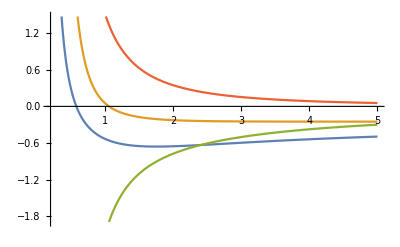

```mathematica
Plot[{1/32(9/Subscript[ω, 0]^7-12/Subscript[ω, 0]^3-3 Subscript[ω, 0]-2 Subscript[ω, 0]^5)-1/(4h)(3/Subscript[ω, 0]^5+1/Subscript[ω, 0]+2 Subscript[ω, 0]^3)+ 1/(8 h^2)(4/Subscript[ω, 0]^3+7 Subscript[ω, 0])/.{Subscript[ω, 0] -> √Tanh[h]},1/32(9/Subscript[ω, 0]^7-12/Subscript[ω, 0]^3-3 Subscript[ω, 0]-2 Subscript[ω, 0]^5)/.{Subscript[ω, 0] -> √Tanh[h]},-1/(4h)(3/Subscript[ω, 0]^5+1/Subscript[ω, 0]+2 Subscript[ω, 0]^3)/.{Subscript[ω, 0] -> √Tanh[h]},+ 1/(8 h^2)(4/Subscript[ω, 0]^3+7 Subscript[ω, 0])/.{Subscript[ω, 0] -> √Tanh[h]}},{h,0.2,5}]
```

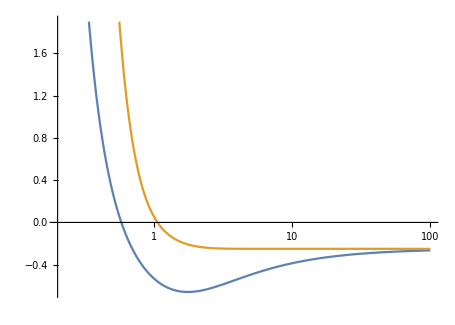

```mathematica
LogLinearPlot[{1/32(9/Subscript[ω, 0]^7-12/Subscript[ω, 0]^3-3 Subscript[ω, 0]-2 Subscript[ω, 0]^5)-1/(4h)(3/Subscript[ω, 0]^5+1/Subscript[ω, 0]+2 Subscript[ω, 0]^3)+ 1/(8 h^2)(4/Subscript[ω, 0]^3+7 Subscript[ω, 0])/.{Subscript[ω, 0] -> √Tanh[h]},1/32(9/Subscript[ω, 0]^7-12/Subscript[ω, 0]^3-3 Subscript[ω, 0]-2 Subscript[ω, 0]^5)/.{Subscript[ω, 0] -> √Tanh[h]},},{h,0.2,100},AspectRatio->1/1.4 ]
```

```mathematica
NSolve[(1/(32 h^2 Subscript[ω, 0]^7)(9 h^2-24 h Subscript[ω, 0]^2+16 Subscript[ω, 0]^4-12 h^2 Subscript[ω, 0]^4-8 h Subscript[ω, 0]^6+28 Subscript[ω, 0]^8-3 h^2 Subscript[ω, 0]^8-16 h Subscript[ω, 0]^10-2 h^2 Subscript[ω, 0]^12)/.{Subscript[ω, 0] -> √Tanh[h]})==0,h,Reals]
```

{{h→0.578819}}

```mathematica
1/(32 h^2 Subscript[ω, 0]^7)(9 h^2-24 h Subscript[ω, 0]^2+16 Subscript[ω, 0]^4-12 h^2 Subscript[ω, 0]^4-8 h Subscript[ω, 0]^6+28 Subscript[ω, 0]^8-3 h^2 Subscript[ω, 0]^8-16 h Subscript[ω, 0]^10-2 h^2 Subscript[ω, 0]^12)//Simplify//Expand
```

```mathematica
Collect[9/(32 Subscript[ω, 0]^7)-3/(4 h Subscript[ω, 0]^5)-3/(8 Subscript[ω, 0]^3)+1/(2 h^2 Subscript[ω, 0]^3)-1/(4 h Subscript[ω, 0])-(3 Subscript[ω, 0])/32+(7 Subscript[ω, 0])/(8 h^2)-Subscript[ω, 0]^3/(2 h)-Subscript[ω, 0]^5/16,{h}]
```

```mathematica
Limit[1/32(9/Subscript[ω, 0]^7-12/Subscript[ω, 0]^3-3 Subscript[ω, 0]-2 Subscript[ω, 0]^5)-1/(4h)(3/Subscript[ω, 0]^5+1/Subscript[ω, 0]+2 Subscript[ω, 0]^3)+ 1/(8 h^2)(4/Subscript[ω, 0]^3+7 Subscript[ω, 0]) /.{Subscript[ω, 0] -> √Tanh[h]},h -> ∞]
```

-1/4

```mathematica
Limit[1/32(9/Subscript[ω, 0]^7-12/Subscript[ω, 0]^3-3 Subscript[ω, 0]-2 Subscript[ω, 0]^5)/.{Subscript[ω, 0] -> √Tanh[h]},h -> ∞]
```

-1/4

```mathematica
D[1/32(9/Subscript[ω, 0]^7-12/Subscript[ω, 0]^3-3 Subscript[ω, 0]-2 Subscript[ω, 0]^5)-1/(4h)(3/Subscript[ω, 0]^5+1/Subscript[ω, 0]+2 Subscript[ω, 0]^3)+ 1/(8 h^2)(4/Subscript[ω, 0]^3+7 Subscript[ω, 0])/.{Subscript[ω, 0]-> √Tanh[h]},h]//Simplify
```

```mathematica
NSolve[1/(512 h^3 Tanh[h]^(9/2))Sech[h]^8 (16 h-152 h^3+(h-282 h^3) Cosh[2 h]-2 h (11+30 h^2) Cosh[4 h]-h Cosh[6 h]-10 h^3 Cosh[6 h]+6 h Cosh[8 h]-18 Sinh[2 h]+84 h^2 Sinh[2 h]+22 Sinh[4 h]+168 h^2 Sinh[4 h]+6 Sinh[6 h]+20 h^2 Sinh[6 h]-11 Sinh[8 h]) ==0,h,Reals]
```

{{h→1.75386}}

```mathematica
1.75386/2/π
```

0.279135

```mathematica
Series[1/32(9/Subscript[ω, 0]^7-12/Subscript[ω, 0]^3-3 Subscript[ω, 0]-2 Subscript[ω, 0]^5) /.{Subscript[ω, 0] -> √Tanh[h]},{h,0,2}]
Series[-1/(4h)(3/Subscript[ω, 0]^5+1/Subscript[ω, 0]+2 Subscript[ω, 0]^3)/.{Subscript[ω, 0] -> √Tanh[h]},{h,0,2}]
Series[+ 1/(8 h^2)(4/Subscript[ω, 0]^3+7 Subscript[ω, 0])/.{Subscript[ω, 0] -> √Tanh[h]},{h,0,2}]
```

9/(32 h^(7/2))-3/(64 h^(3/2))-(213 √h)/1280+O[h]^(5/2)

-3/(4 h^(7/2))-7/(8 h^(3/2))-(21 √h)/32+O[h]^(5/2)

```mathematica
1/(2 h^(7/2))+9/(8 h^(3/2))-(17 √h)/120+O[h]^(5/2)
9/32-24/32+16/32
```

1/(2 h^(7/2))+9/(8 h^(3/2))-(17 √h)/120+O[h]^(5/2)

1/32